```mathematica
Remove["Global`*"]
```

```mathematica
WPM=40;WPL=30;WPL=15;
(**)
```

```mathematica
q = 51; V0=(204/100)*10^(-8);
t0 = (q*(3*q-1)/V0)^(1/2);ϕ0=1; dϕ0=N[(((2*q)^(1/2))/t0),60];Ni=0;Nf=70;
```

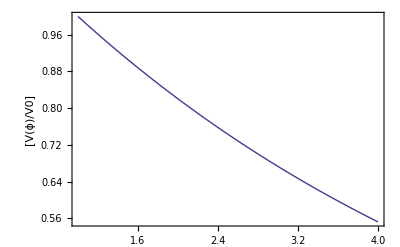

```mathematica
V[ϕ_] = V0*Exp[-((2/q)^(1/2))*(ϕ-ϕ0)];
DV[ϕ_] = D[V[ϕ],ϕ];
Plot[(V[ϕ]/V0),{ϕ,ϕ0,4},PlotRange->All,Frame->True, FrameLabel->{"[V(ϕ)/V0]"}]
```

```mathematica
H0 = ((1/3)*((dϕ0^2/2)+V[ϕ0]))^(1/2);
Dϕ0 = (dϕ0/H0);
```

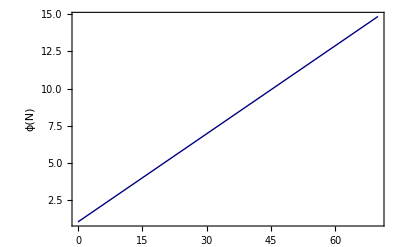

```mathematica
ϕSoln=NDSolve[{ϕ''[N]+(3-ϕ'[N]^2/2)*ϕ'[N]+(DV[ϕ[N]]/(2*V[ϕ[N]]))*(6-(ϕ'[N])^2)==0,ϕ[Ni]==ϕ0,ϕ'[Ni]==Dϕ0},ϕ,{N,Ni,Nf},MaxSteps->1000000, WorkingPrecision->WPM];
ϕ[N_]=ϕ[N]/.Flatten[ϕSoln];
Plot[ϕ[N],{N,Ni,Nf},Frame->True,PlotRange->All,FrameLabel->{"ϕ(N)"},PlotStyle->{Darker[Blue,0.5]}]
```

```mathematica
Export["~/Github/project_work/power_law/mathematica_codes/phi_vs_N_mathematica.txt",Table[{N,ϕ[N]},{N,Ni,Nf,(Nf-Ni)/100000}]];
```

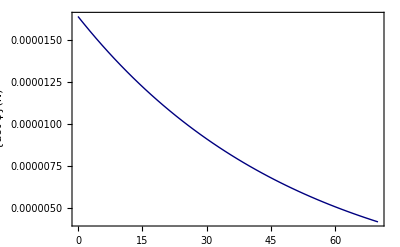

```mathematica
H[N_]=(V[ϕ[N]]/(3-((ϕ'[N])^2)/2))^(1/2);
Plot[{H[N]*ϕ'[N]},{N,Ni,Nf},Frame->True, PlotRange->All, FrameLabel->{"{dot ϕ}(N)"},PlotStyle->{Darker
[Blue,0.5]}]
```

```mathematica
Export["~/Github/project_work/power_law/mathematica_codes/H_vs_N_mathematica.txt",Table[{N,H[N]},{N,Ni,Nf,(Nf-Ni)/100000}]];
```

```mathematica
Export["~/Github/project_work/power_law/mathematica_codes/DH_vs_N_mathematica.txt",Table[{N,H'[N]},{N,Ni,Nf,(Nf-Ni)/100000}]];
```

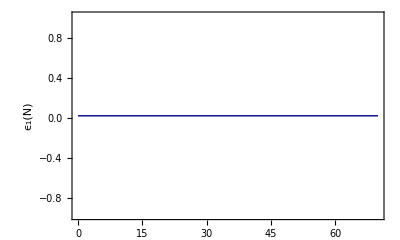

```mathematica
ϵ1[N_] =((ϕ'[N])^2/2);
Plot[ϵ1[N],{N,Ni,Nf},Frame->True, PlotRange->All, AspectRatio->0.6,FrameLabel->{"\!\(\*SubscriptBox[\(ϵ\),\(1\)]\)(N)"},PlotStyle->{Darker[Blue, 0.5]}]
```

```mathematica
Export["~/Github/project_work/power_law/mathematica_codes/eps_vs_N_mathematica.txt",Table[{N,ϵ1[N]},{N,Ni,Nf,(Nf-Ni)/100000}]];
```